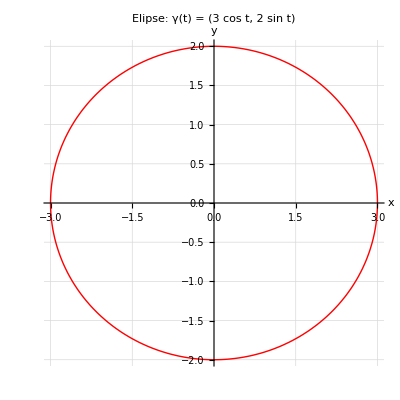

```mathematica
(*Parámetros de la elipse*)a=3;    (*semieje mayor*)
b=2;    (*semieje menor*)

(*Graficar la elipse parametrizada γ(t)=(a Cos[t],b Sin[t])*)
ParametricPlot[{a*Cos[t],b*Sin[t]},{t,0,2*Pi},PlotRange->All,AxesLabel->{"x","y"},AspectRatio->1,PlotStyle->{Thick,Red},GridLines->Automatic,PlotLabel->"Elipse: γ(t) = ("<>ToString[a]<>" cos t, "<>ToString[b]<>" sin t)"]
```